```mathematica
finala = {
{0,1,1,0,0,0,0,0,0,0},{0,0,0,1,1,0,0,0,0,0},
{0,0,0,0,1,1,0,0,0,0},{0,0,0,0,0,0,1,1,0,0},{0,0,0,0,0,0,0,1,1,0},{0,0,0,0,0,0,0,0,1,1},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}};
```

```mathematica
testm = {Upstate[0,0], Upstate[Pi/2,0],Downstate[Pi/2,0],Upstate[0,0],Downstate[0,0],Upstate[Pi/2,Pi/2],Downstate[Pi/2,Pi/2], Upstate[Pi/2,Pi/4],Downstate[Pi/2,Pi/4],Upstate[Pi/4,Pi/4],Downstate[Pi/4,Pi/4], Upstate[Pi/4,-Pi/4],Downstate[Pi/4,-Pi/4] } ;
```

```mathematica
l={"(0, 0)","(π/2, 0)","(0, 0)","(π/2, π/2)","(π/4, π/2)","(π/4,π/4)","(π/4,-π/4)",Null,Null,Null, Null};
```

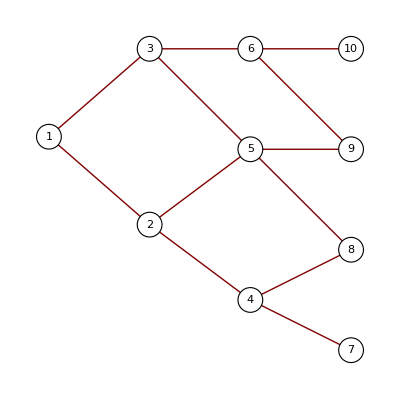

```mathematica
TreePlot[finala,Left,VertexRenderingFunction->({White,EdgeForm[Black],Tooltip[Disk[#,.1],l[[#2]]],Black,Text[#2,#1]}&),DirectedEdges->True]
```

```mathematica
(*singlepathes*)
testp = {{1,2,4,8},{1,3,7,13}};
```

```mathematica
GetPs[testm,testp] //N
```

{0.125,0.0625}

```mathematica
(*multipathes*)
```

```mathematica
SumGetPs[testm,{{1,2,4,9},{1,2,5,10},{1,3,6,10}}] //N
```

0.349112

```mathematica
SumGetPs[testm,{{1,2,5,11},{1,3,6,11},{1,3,7,12}}] //N
```

0.463388

```mathematica
(*adds up to one... kinda*)
.213388+.0625+.260723+.463388
```

0.999999

```mathematica
(*second part*)
SumGetPs[testm,{{1,2,4,9},{1,2,5,10},{1,2,5,11},{1,3,6,10},{1,3,6,11}}] //N
```

0.625

```mathematica
SumGetPs[testm,{{1,3,7,12}}] //N
```

0.1875

```mathematica
(*adds up to once really nicely.*)
.625+.1875+.125+.0625
```

1.